### Base case: constant growth c1 & constant sloughing c2<c1

#### Setup

```mathematica
ClearAll["Global`*"];Remove["Global`*"];

RodOde[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=Block[{x,y,θ,m,S},
sol=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x,y,θ,m},{S,0,LR}][[1]];
{x[S]-L0,y[S],θ[S]}/.sol/.S->LR];

RodShape[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x[S],y[S],θ[S],m[S]},{S,0,LR}][[1]];
```

#### Evolving shape

Parameters

```mathematica
L0=1;
Subscript[c, 1]=1.2; (* growth rate *)
Subscript[c, 2]=1; (* sloughing rate *)
dt=0.1;
```

First step

```mathematica
i=1;
t=i dt;
γ=1+Subscript[c, 1] t;
LR=L0-(Subscript[c, 2] t)/(1+Subscript[c, 1] t);
```

```mathematica
Subscript[S, 1]=FindRoot[RodOde[a,b,c,LR],{a,-5},{b,-2},{c,0.1}]
```

{a→-9.5804,b→-0.865767,c→0.180737}

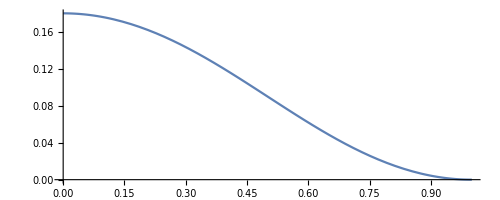

```mathematica
Subscript[Sol, 1]=RodShape[a/. Subscript[S, 1],b/. Subscript[S, 1],c/. Subscript[S, 1],LR];
ParametricPlot[Evaluate[{x[S],y[S]}/. Subscript[Sol, 1]],{S,0,LR}]
```

Now iterate

```mathematica
NN=10;
For[i=2,i≤NN,i++,
t=i dt;
γ=1+Subscript[c, 1] t;
LR=L0-(Subscript[c, 2] t)/(1+Subscript[c, 1] t);
Subscript[S, i]=FindRoot[RodOde[a,b,c,LR],{a,a/. Subscript[S, i-1]},{b,b/. Subscript[S, i-1]},{c,c/. Subscript[S, i-1]}];
]
```

```mathematica
Manipulate[t=i dt;
γ=1+Subscript[c, 1] t;
LR=L0-(Subscript[c, 2] t)/(1+Subscript[c, 1] t);
Sol=RodShape[a/. Subscript[S, i],b/. Subscript[S, i],c/. Subscript[S, i],LR];
ParametricPlot[Evaluate[{x[S],y[S]}/.Sol],{S,0,LR}],{i,1,NN,1}]
```

### Eventual steady state: constant growth c1 & ramped sloughing up to c1

#### Setup

```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]

(*RodOde[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=Block[{x,y,θ,m,S},
sol=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x,y,θ,m},{S,0,LR}][[1]];
{x[S]-L0,y[S],θ[S]}/.sol/.S->LR];

RodShape[nx_?NumberQ,m0_?NumberQ,y0_?NumberQ,LR_]:=NDSolve[{
x'[S]==γ Cos[θ[S]],
y'[S]==γ Sin[θ[S]],
θ'[S]==γ m[S],
m'[S]==γ nx Sin[θ[S]],
x[0]==0,y[0]==y0,θ[0]==0,m[0]==m0},{x[S],y[S],θ[S],m[S]},{S,0,LR}][[1]];*)
```

```mathematica
RodOde[R:{__?NumericQ},LR_]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,LR}][[1]];
{x[S]-0.5,y[S],θ[S]}/.Sol/.S->LR
];

EquilSol[R_,LR_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,m,nx,ny},{S,0,LR}][[1]];
```

#### Evolving shape

Parameters

```mathematica
NIntegrate[W[S],{S, 0, 0.5}]
```

0.141795

```mathematica
L0=1;
Subscript[c, 1]= 0.14179490475200954;(* growth rate *)
σ=10; (* sloughing rate *)
As=2.5;
dt=0.05;
w = 0.010;
L0=0.125;
h = 0.015;
kf =0.01;
k=(12*kf*L0^4)/(w*h^3);
W=Function[s,Exp[-(s/0.16)^2]];
```

Sloughing rate function

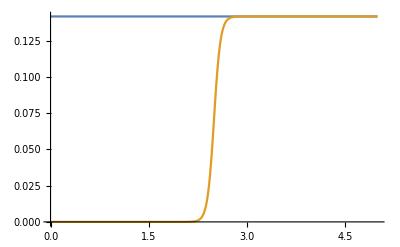

```mathematica
μ[σ_,AL_,As_]:=Subscript[c, 1] 1/2(1.0+Tanh[σ(AL-As)]);
Plot[{Subscript[c, 1],μ[σ,AL,As]},{AL,0,5.0}]
```

```mathematica
(* Initialise *)
LR = 0.5;
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
η=10;
γ[S_]:=1+dt*W[S];
(*g = 1+dt;*)
(*γ[S_]=g;*)
px[S_]:=S;
py[S_]:=0;
A[S_]:=0;
R0 = {-98.076656061,0.033509647981,-0.98707211693};
```

{R→{-98.0508,0.0712413,-2.10738}}

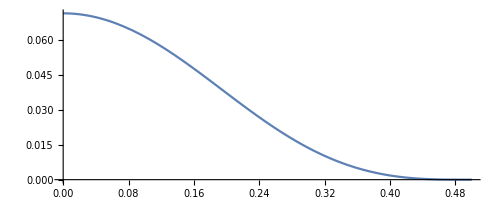

```mathematica
Sol=FindRoot[RodOde[R,LR],{R, R0}]
sol=EquilSol[R/.Sol,LR];
ParametricPlot[Evaluate[{x[S],y[S]}/.sol],{S,0,LR}]
```

```mathematica
grs={};
(* first step *)
γ[S_]=1+dt*W[S];
(*g = 1+dt;
γ[S_]= g;*)
Sol=FindRoot[RodOde[R,LR],{R,R/.Sol}];
sol=EquilSol[R/.Sol,LR];
rs=R/.Sol;
AppendTo[grs,{γ,LR,A,k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,LR}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,LR}];
AOld = A;
ANew = FunctionInterpolation[(AOld[S]*(1 - dt*W[s[S]/.sol]))+dt,{S, 0, LR}];
A = ANew;
```

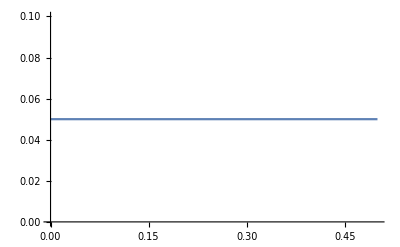

```mathematica
Plot[A[S],{S, 0, LR}]
```

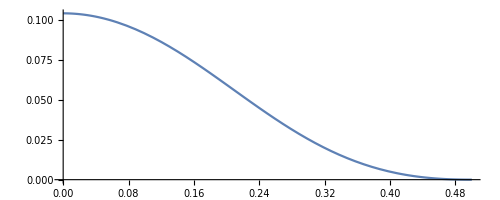

```mathematica
(* Second step *)
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
(*g=g*(1+dt);*)
(*γ[S_]=g;*)
Sol=FindRoot[RodOde[R,LR],{R,R/.Sol}];
sol=EquilSol[R/.Sol,LR];
re=R/.Sol;
AppendTo[grs,{γ,LR,A,k,rs,sol,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,LR}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,LR}];
ParametricPlot[{x[S],y[S]}/.sol,{S,0,LR}]
Clear[AOld,ANew];
AOld = A;
ANew = FunctionInterpolation[(AOld[S]*(1 - dt*W[s[S]/.sol]))+dt,{S, 0, LR}];
A=ANew;
```

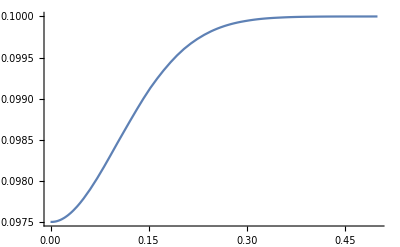

```mathematica
Plot[A[S],{S, 0, LR}]
```

```mathematica
Clear[LROld,LRNew];
LROld = LR;
LRNew=LROld-dt*Subscript[c, 1] 1/2(1.0+Tanh[σ((A[S]/.S-> LROld)-As)]);
LR=LRNew;
```

```mathematica
(* Iterate over now *)
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.3;
MaxFails=60;
(*
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,L/2}]];*)
P1=Plot[γ[S],{S,0,LR},PlotRange-> Full];
P2=Plot[A[S],{S,0,LR}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
rd
While[flag==0,
t = (re - rs);
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.sol,{S,k}],{k, 0, 1}]],{S, 0,LR}];

γ=γNew;
(*g=g*(1+dt);
γ[S_]=g;*)
Sol=Quiet[Reap[FindRoot[RodOde[R,LR],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOde[R/.Sol[[1]],LR]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
γ=γOld;
(*g=g/(1+dt);*)
dt = 0.5* dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
sol=EquilSol[R/.Sol[[1]],LR];
rs = re;
re = R/.Sol[[1]];
AppendTo[grs,{γ,LR,A,k,rs,sol,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.sol,{S,0,LR}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.sol,{S,0,LR}];
Clear[AOld,ANew];
AOld = A;
ANew = FunctionInterpolation[(AOld[S]*(1 - dt*W[s[S]/.sol]))+dt,{S, 0, LR}];
A=ANew;
Clear[LROld,LRNew];
LROld = LR;
LRNew=LROld-dt*Subscript[c, 1] 1/2(1.0+Tanh[σ((AOld[S]/.S-> LROld)-As)]);
LR=LRNew;
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.sol,{S,0,LR},PlotRange-> Full]];
(*P1 = Plot[γ[S],{S, 0, L/2}];*)
P2=Plot[A[S],{S,0,LR}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[Sol[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt];];
];

];
```

rd

0.025

0.0305176

0.0190735

0.00953674

0.00476837

0.00238419

0.00710543

0.00355271

0.00222045

0.00529396

0.00330872

0.00165436

0.00129247

0.000646235

0.000631089

0.000315544

0.00117549

0.000587747

0.000367342

0.000560519

0.000547382

0.000273691

0.000522024

0.000509789

0.00189911

0.00148368

0.00115913

0.00141495

0.00110543

0.00263555

0.00205902

0.00201076

0.00306818

0.00153409

0.000958807

0.000749068

0.000468168

0.00139525

0.000697624

0.000348812

0.000218008

0.000266122

0.000133061

0.0000665306

0.0000332653

0.0000166327

0.0000129943

6.49713×10^-6

3.24857×10^-6

1.62428×10^-6

8.12141×10^-7

4.06071×10^-7

2.03035×10^-7

$Aborted

```mathematica
Length[grs]
```

352

```mathematica
Log[grs[[11,1]][0]]
```

0.512594

```mathematica
Manipulate[ParametricPlot[{x[S],y[S]}/.grs[[i,6]],{S,0,grs[[i,2]]},PlotRange->All],{i,2,Length[grs],1}]
```

```mathematica
Manipulate[Plot[grs[[i,3]][S],{S,0,grs[[i,2]]},PlotRange->All],{i,2,Length[grs],1}]
```

Part::partd: Part specification grs ⟦ 244, 3 ⟧ is longer than depth of object.

Part::partd: Part specification grs ⟦ 244, 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Plot::plln: Limiting value grs ⟦ 244, 2 ⟧ in {S, 0, grs ⟦ FE`i$$40, 2 ⟧} is not a machine-sized real number.

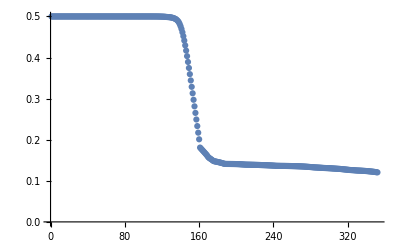

```mathematica
ListPlot[Table[grs[[i,2]],{i, 1, Length[grs]}]]
```

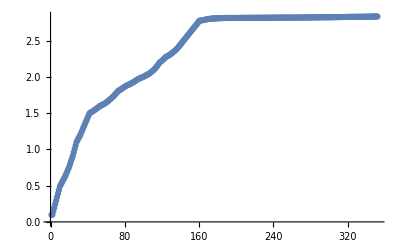

```mathematica
ListPlot[Table[Log[grs[[i,1]][0]],{i, 1, Length[grs]}]]
```

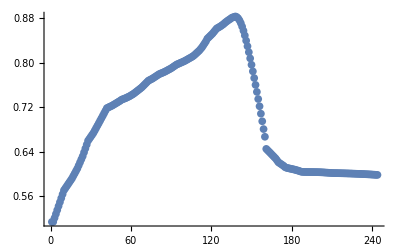

```mathematica
ListPlot[Table[NIntegrate[grs[[i,1]][S],{S, 0, grs[[i,2]]}],{i, 1, Length[grs]}]]
```

```mathematica
ListPlot[Table[{Log[grs[[i,1]][0]],grs[[i,2]]},{i,0, Length[grs]}]]
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

```mathematica
SloughingData = Table[{Log[grs[[i,1]][0]],grs[[i,2]],NIntegrate[grs[[i,1]][S],{S, 0, grs[[i,2]]}]},{i, 1, Length[grs]}];
```

```mathematica
Export["~/Documents/MorphoCrypt/Mathematica/Solutions/agedbasedsloughing.csv", SloughingData,"CSV"];
```

```mathematica
Log[grs[[Length[grs],1]][0]]
```

2.81914

```mathematica
S0Mesh = Range[0, 0.5, 0.001];
```

```mathematica
Log[grs[[170,1]][0]]
```

2.80011

```mathematica
grs[[170,2]]
```

0.157011

```mathematica
S0Mesh = Range[0, 0.5, grs[[170,2]]]
```

{0.,0.157011,0.314022,0.471033}

```mathematica
S0Mesh = Range[0, grs[[170,2]],0.001];
```

```mathematica
data=Table[0.5*(({x[S0Mesh[[i]]], y[S0Mesh[[i]]]}/.grs[[170, 6]]) + ({x[S0Mesh[[i]]], y[S0Mesh[[i]]]}/.grs[[170,6]])),{i, 1, Length[S0Mesh]}];
Export["~/Documents/MorphoCrypt/Mathematica/Solutions/sols_agedbasedsloughing_T_2p8.csv",data, "CSV"];
```